### Variando b2 , b0=1Radio del Sol θMin=0.008

```mathematica
(*Variando b2*)
```

```mathematica
Quit[]
```

```mathematica
(* Ecuaciones Utilez *)
angu2[δ_,ϕ2_,b1_,b3_, Λ_,G_,M_,c_]:=(4 G M)/c^2(-Cos[ϕ2]/b1+(Cos[δ+ϕ2]+Sin[δ])/b3)+1/2 (G M)/c^2 Λ (4 (b1-b3 Cos[δ]) Cos[ϕ2]-(2 b1)/(1+Cos[ϕ2])+(2 b3)/(-1+Cos[δ+ϕ2])+b1 Csc[ϕ2/2]^2+b3 (Sec[(δ+ϕ2)/2]^2+4 Sin[δ] Sin[ϕ2]-2 (3+Cos[2 δ]) Sec[δ] Tan[δ]))+1/32 (G M)/c^2 Λ^2 (12 (b1^3 (Log[-Cos[ϕ2/2]]+Log[Cos[ϕ2/2]]-Log[-Sin[ϕ2/2]]-Log[Sin[ϕ2/2]])+b3^3 (Log[-Cos[1/4 (π+2 δ)]]+Log[Cos[1/4 (π+2 δ)]]-Log[-Cos[(δ+ϕ2)/2]]-Log[Cos[(δ+ϕ2)/2]]-Log[-Sin[1/4 (π+2 δ)]]-Log[Sin[1/4 (π+2 δ)]]+Log[Sin[1/2 (-δ-ϕ2)]]+Log[Sin[(δ+ϕ2)/2]]))-(Csc[δ+ϕ2]^2 Sec[δ]^2 Sin[ϕ2]^2 (b1^3 Cos[δ]^4 (-32 Cos[ϕ2]-17 Cos[3 ϕ2]+Cos[5 ϕ2]) Csc[ϕ2]^4 Sin[δ+ϕ2]^4-b3^3 (Cos[δ]^5 (-32 Cos[ϕ2]+(17-34 Cos[2 δ]) Cos[3 ϕ2]+(1-2 Cos[2 δ]+2 Cos[4 δ]) Cos[5 ϕ2])+Cos[δ]^4 (32 Sin[δ] Sin[ϕ2]+17 Sin[3 δ] Sin[3 ϕ2]-Sin[5 δ] Sin[5 ϕ2])+(-32 Sin[δ]+17 Sin[3 δ]+Sin[5 δ]) Sin[δ+ϕ2]^4)))/((-1+Cos[ϕ2]) (1+Cos[ϕ2]) (-1+Cos[δ+ϕ2]) (1+Cos[δ+ϕ2]) (-1+Sin[δ]) (1+Sin[δ])))+(G^2 M^2)/c^4(15 (b1-b3) (b1+b3) (π-2 ϕ2)+b3^2 Sin[2 ϕ2]-2 b1^2 Cos[ϕ2] Sin[2 δ+ϕ2])/(4 b1^2 b3^2)+1/8 (G^2 M^2)/c^4 Λ (Cot[ϕ2] (30-32 Csc[ϕ2]^2)+Cot[δ+ϕ2] (-30+32 Csc[δ+ϕ2]^2)+15 ((π-2 ϕ2) Csc[ϕ2]^2+(-π+2 (δ+ϕ2)) Csc[δ+ϕ2]^2-2 δ Sec[δ]^2)+2 (-14+Cos[2 δ]+Cos[2 ϕ2]+Cos[2 (δ+ϕ2)]+16 Sec[δ]^2) Tan[δ])+3/32 (G^2 M^2)/c^4 Λ^2 (-2 b3^2 Cot[δ+ϕ2] (8-47 Csc[δ+ϕ2]^2+32 Csc[δ+ϕ2]^4)+b3^2 (3 (π-2 (δ+ϕ2)) (1+4 Cos[2 (δ+ϕ2)]) Csc[δ+ϕ2]^4-1/2 Sec[δ]^5 (12 δ Cos[δ]+24 δ Cos[3 δ]+85 Sin[δ]-41 Sin[3 δ]+2 Sin[5 δ]))+1/2 b1^2 Csc[ϕ2]^5 (85 Cos[ϕ2]+41 Cos[3 ϕ2]+2 Cos[5 ϕ2]+6 (π-2 ϕ2) (Sin[ϕ2]-2 Sin[3 ϕ2]))-16 (b3^2 Cos[δ] Log[Cot[1/4 (π+2 δ)]]+b1^2 Log[Cot[ϕ2/2]] Sin[ϕ2]+b3^2 Log[Tan[(δ+ϕ2)/2]] Sin[δ+ϕ2])); (*Solución serie*)

Eq=-1-Λ̄+(Λ̄)/u[ϕ]^2+Rs Λ̄ u[ϕ]+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2==0;(*Ecuación de la geodésica*)

Ang[ϕ_,Rs_,Lb_]:=ArcTan[ -(u[ϕ] √(1-Lb/u[ϕ]^2) √(1-Rs u[ϕ]))/u'[ϕ]];
(*conversión coordenadas*)
xf[ϕ_]:=Cos[ϕ]/u[ϕ];
yf[ϕ_]:=Sin[ϕ]/u[ϕ];
```

```mathematica
(*Cantidades Físicas, Tomando una Masa solar*)
Λf =10^-27;(*m^-2 1.1056 10^-52 *)
Msun=1.9885*10^30;(*kg*)
Rsun=6.96*10^8;(*m*)
Gf=6.674*10^-11;(*m^3 kg^-1 s^-2*)
c=299792458;(*m/s*)
M=1*Msun;
M2=0;
RSch=2Gf M/c^2 ;(*Sch radio -> m*)
RSchF=2Gf M2/c^2;
```

```mathematica
aVal={1.1,1.52,2.4,3.45,4.5,5.0,6,8,9,10,12,13.8,15.85,16.7,18,23,27.3,31.2,36.52,46.8,54.2,63,74.65,82.8}; (*{1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,2,2.1,2.2, 2.3,2.4,2.5, 2.51,2.52,2.53, 2.54,2.55,2.56, 2.561, 2.562,2.563,2.564}*)
```

1.1

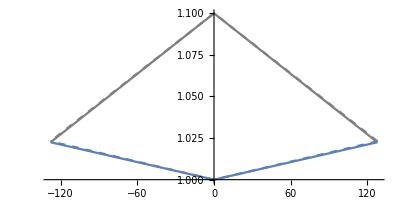

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

InterpolatingFunction::dmval: Input value {-29.1123} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0909982} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.5213} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

posición b2, b3{{ϕ→1.5773}}{ϕ→1.56429}0.008

1.52

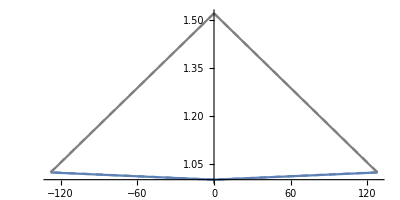

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

posición b2, b3{{ϕ→1.56691}}{ϕ→1.57468}0.008

2.4

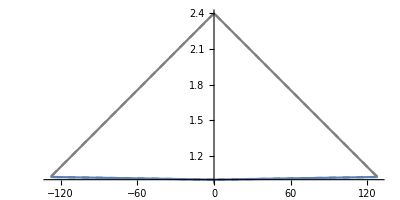

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve::ifun will be suppressed during this calculation.

posición b2, b3{{ϕ→1.56002}}{ϕ→1.58158}0.008

3.45

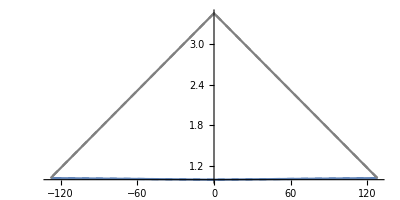

posición b2, b3{{ϕ→1.57938}}{ϕ→1.56221}0.008

4.5

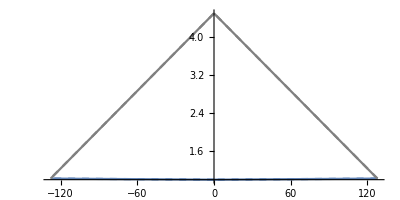

posición b2, b3{{ϕ→1.5436}}{ϕ→1.59799}0.008

5.

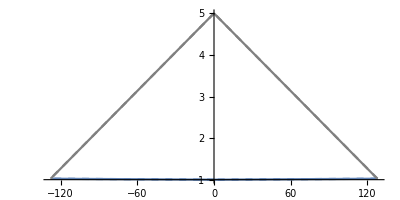

posición b2, b3{{ϕ→1.53967}}{ϕ→1.60192}0.008

6

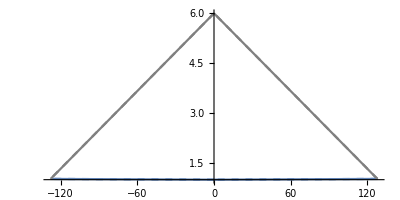

posición b2, b3{{ϕ→1.53183}}{ϕ→1.60976}0.008

8

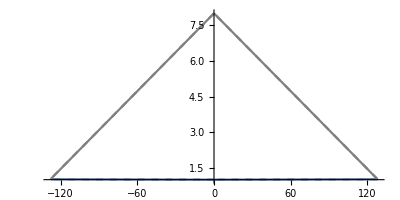

posición b2, b3{{ϕ→1.51616}}{ϕ→1.62543}0.008

9

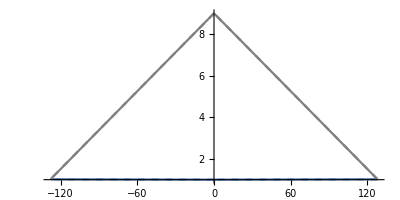

posición b2, b3{{ϕ→1.50832}}{ϕ→1.63327}0.008

10

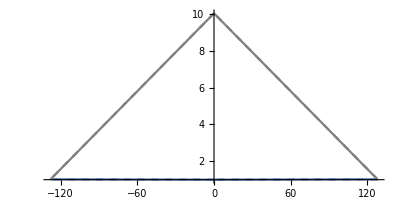

posición b2, b3{{ϕ→1.50048}}{ϕ→1.64112}0.008

12

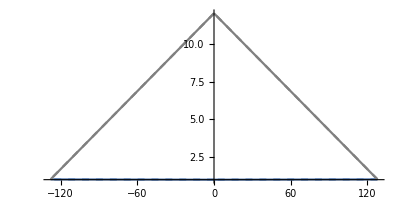

posición b2, b3{{ϕ→1.48477}}{ϕ→1.65682}0.008

13.8

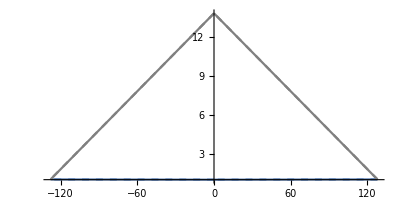

posición b2, b3{{ϕ→1.47062}}{ϕ→1.67098}0.008

15.85

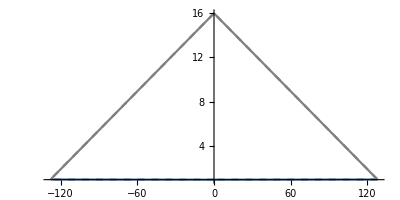

posición b2, b3{{ϕ→1.45447}}{ϕ→1.68712}0.008

16.7

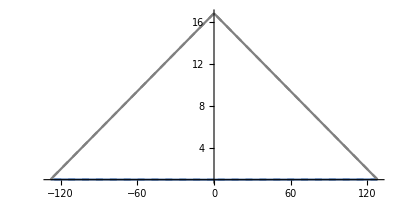

posición b2, b3{{ϕ→1.44776}}{ϕ→1.69383}0.008

18

NDSolve::ndcf: Repeated convergence test failure at ϕ == 1.4768; unable to continue.

NDSolve::ndcf: Repeated convergence test failure at ϕ == 1.66479; unable to continue.

General::stop: Further output of NDSolve::ndcf will be suppressed during this calculation.

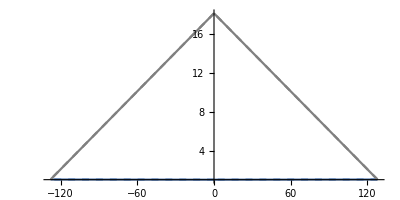

posición b2, b3{{ϕ→1.43749}}{ϕ→1.7041}0.008

23

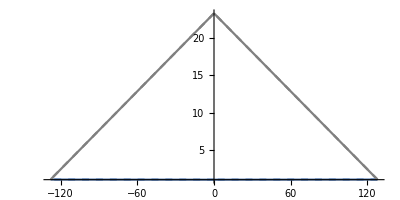

posición b2, b3{{ϕ→1.39786}}{ϕ→1.74373}0.008

27.3

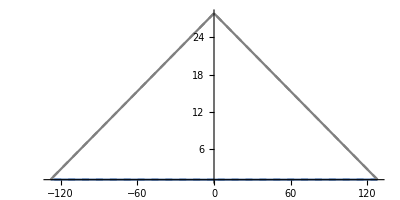

posición b2, b3{{ϕ→1.36354}}{ϕ→1.77805}0.008

31.2

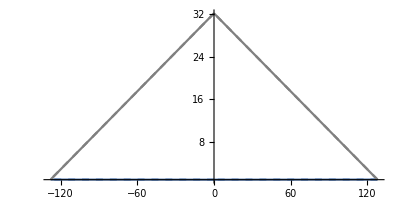

posición b2, b3{{ϕ→1.33221}}{ϕ→1.80939}0.008

36.52

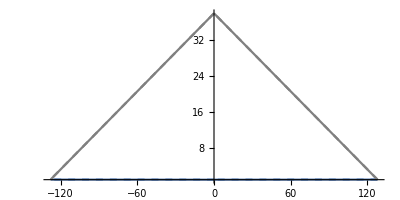

posición b2, b3{{ϕ→1.28903}}{ϕ→1.85256}0.008

46.8

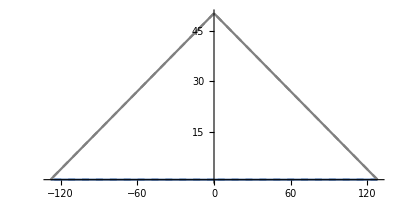

posición b2, b3{{ϕ→1.20393}}{ϕ→1.93767}0.008

54.2

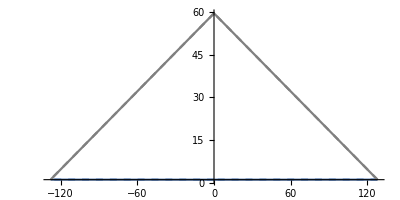

posición b2, b3{{ϕ→1.14088}}{ϕ→2.00071}0.008

63

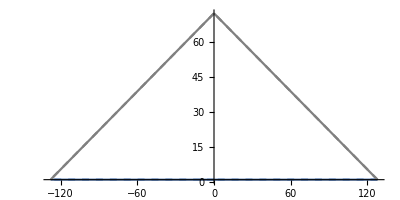

posición b2, b3{{ϕ→1.06337}}{ϕ→2.07822}0.008

74.65

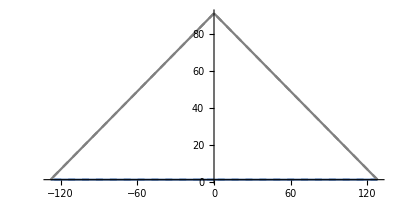

posición b2, b3{{ϕ→0.95508}}{ϕ→2.18651}0.008

82.8

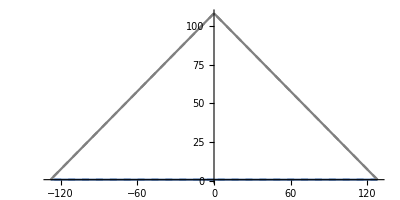

posición b2, b3{{ϕ→0.874075}}{ϕ→2.26752}0.008

```mathematica
DatAngN={};
DatAngSe={};
DataTriang={};
DataTriangFond={};
DatAngb2Pos={};
Do[
a=aVal[[i]];
Print[a];
(*C1*)
b0 =Rsun;(*m*)
Rsval1=RSch/b0;(*Rs=rs/b*)
Rsval1F=RSchF/b0;(*Rs=rs/b*)
Lval1=Λf*b0^2; (*Λ̄ = Λ b^2 -> *)
ϕMin1=0.008;
ϕMax1=π-ϕMin1;
δval=0;

(*Geodesic C1*)(*Print["c1"];*)

(*Metrica*)
sol1=NDSolve[{Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1[[1]];
sol12=NDSolve[{Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]; (*[π/2, ϕMax]*)

(*Fondo*)
sol1F=NDSolve[({Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1F[[1]];
sol12F=NDSolve[({Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Geodesic C2*)(*Print["c2"];*)
b1 =a*b0;(*m*)
Rsval2=RSch/b1;(*Rs=rs/b*)
Rsval2F=RSchF/b1;
Lval2=Λf*b1^2; (*Λ̄ = Λ b^2 -> *)
ϕMin2=ϕMin1;
ϕMax2=π/2;

(*Metrica*)
temp=(u[ϕMin2]*b1/b0)/.sol1[[1]];
sol2=NDSolve[{Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2},{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)

(*Fondo*)
temp=(u[ϕMin2]*b1/b0)/.sol1F[[1]];
sol2F=NDSolve[({Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2F}),{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];

(*Geodesic C2*)(*Print["c3"];*)
b2 =a*b0;(*m*)
Rsval3=RSch/b2;(*Rs=rs/b*)
Rsval3F=RSchF/b2;
Lval3=Λf*b2^2; (*Λ̄ = Λ b^2 -> *)
ϕMin3=ϕMax2;
ϕMax3=ϕMax1;

(*Metrica*)
temp=(u[ϕMax3]*b2/b0)/.sol12[[1]];
sol3=NDSolve[{Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3},{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Fondo*)
temp=(u[ϕMax3]*b2/b0)/.sol12F[[1]];
sol3F=NDSolve[({Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3F}),{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Construyendo tríangulos*)
DatTr={};
DatTrF={{},{},{}};
C1ϕvalor=Subdivide[ϕMin1,ϕMax1, 1000];
C2ϕvalor=Subdivide[ϕMin2,ϕMax2, 1000];
C3ϕvalor=Subdivide[ϕMin3,ϕMax3, 1000];
Do[
AppendTo[DatTr,{C1ϕvalor[[i]],
			    If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1[[1]],xf[C1ϕvalor[[i]]]/.sol12[[1]]], 
			    If[C1ϕvalor[[i]]<=π/2,yf[C1ϕvalor[[i]]]/.sol1[[1]],yf[C1ϕvalor[[i]]]/.sol12[[1]]],
			    C2ϕvalor[[i]],
			    b1/b0*xf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    b1/b0*yf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    C3ϕvalor[[i]],
			    b2/b0*xf[C3ϕvalor[[i]]]/.sol3[[1]],
			    b2/b0*yf[C3ϕvalor[[i]]]/.sol3[[1]]}];

(*Fondo*)
AppendTo[DatTrF,{C1ϕvalor[[i]],
			       If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1F[[1]],xf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      If[C1ϕvalor[[i]]<=π/2, yf[C1ϕvalor[[i]]]/.sol1F[[1]], yf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      C2ϕvalor[[i]],
			      b1/b0*xf[C2ϕvalor[[i]]]/.sol2F[[1]],
			      b1/b0*yf[C2ϕvalor[[i]]]/.sol2F[[1]],C3ϕvalor[[i]],
			      b2/b0*xf[C3ϕvalor[[i]]]/.sol3F[[1]], 
			      b2/b0*yf[C3ϕvalor[[i]]]/.sol3F[[1]]}];
,{i,1,Length[C1ϕvalor]}];

(*Graficandolos*)

Pc1=ParametricPlot[{xf[ϕ]/.sol1[[1]],yf[ϕ]/.sol1[[1]]},{ϕ,ϕMin1,π/2}, PlotRange->All,AspectRatio->0.5];
Pc12=ParametricPlot[{xf[ϕ]/.sol12[[1]],yf[ϕ]/.sol12[[1]]},{ϕ,π/2,ϕMax1}, PlotRange->All,AspectRatio->0.5];
Pc2=ParametricPlot[{b1/b0*xf[ϕ]/.sol2[[1]],b1/b0*yf[ϕ]/.sol2[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->Gray,AspectRatio->1];
Pc3=ParametricPlot[{b2/b0*xf[ϕ]/.sol3[[1]],b2/b0*yf[ϕ]/.sol3[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->Gray,AspectRatio->1];

Pc1F=ParametricPlot[{xf[ϕ]/.sol1F[[1]],yf[ϕ]/.sol1F[[1]]},{ϕ,ϕMin1,π/2}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc12F=ParametricPlot[{xf[ϕ]/.sol12F[[1]],yf[ϕ]/.sol12F[[1]]},{ϕ,π/2,ϕMax1}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc2F=ParametricPlot[{b1/b0*xf[ϕ]/.sol2F[[1]],b1/b0*yf[ϕ]/.sol2F[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];
Pc3F=ParametricPlot[{b2/b0*xf[ϕ]/.sol3F[[1]],b2/b0*yf[ϕ]/.sol3F[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];

Print[Show[{Pc1,Pc12,Pc2, Pc3,Pc1F,Pc12F,Pc2F,Pc3F},PlotRange->All]];

(*Calculando angulos*)
ptos={ϕMax1,π/2,ϕMin1};
(*C1*)
angC1 = Last[{Ang[ptos[[1]],Rsval1,Lval1]/.sol12,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1];
angC1F = Last[{Ang[ptos[[1]],Rsval1F,Lval1]/.sol12F,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1F];
(*C2*)
angC2= Last[{Ang[ptos[[-1]],Rsval2,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2];
angC2F = Last[{Ang[ptos[[-1]],Rsval2F,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2F];
(*C3*)
angC3= Last[{Ang[ptos[[2]],Rsval3,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3];
angC3F = Last[{Ang[ptos[[2]],Rsval3F,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3F];
(*Betas*)
betas = {angC3[[2]]-angC1[[1]], angC1[[2]]-angC2[[1]],-angC3[[1]]+angC2[[2]]};
betasF = {angC3F[[2]]-angC1F[[1]], angC1F[[2]]-angC2F[[1]],-angC3F[[1]]+angC2F[[2]]};
(*Serie*)
delI=NSolve[(u'[ϕ]/.sol2[[1]])==0,ϕ];
delI2=FindRoot[(u'[ϕ]/.sol3[[1]])==0,{ϕ,ϕMax3}];
Print["posición b2, b3",delI,delI2, ϕMin1];
delt=π/2-ϕ/.delI;
ASer=Last@angu2[delt,ϕMin1,b0,b2, Λf,Gf,M,c];
(*Salvando*)
AppendTo[DataTriang,DatTr];
AppendTo[DataTriangFond,DatTrF];
AppendTo[DatAngN,{a,Abs[Last@Total[betas-betasF]]}];
AppendTo[DatAngSe,{a,Abs@ASer}];
AppendTo[DatAngb2Pos,{a,ϕ/.delI[[1]]}],
{i, 1,Length[aVal]}
]
```

```mathematica
{aVal[[1]],aVal[[6]],aVal[[11]],aVal[[16]],aVal[[23]]}
```

{1.1,5.,12,23,74.65}

```mathematica
Export["dataTriang1b2_0_008.dat", DataTriang[[1]]]
Export["dataTriang2b2_0_008.dat", DataTriang[[6]]]
Export["dataTriang3b2_0_008.dat", DataTriang[[11]]]
Export["dataTriang4b2_0_008.dat", DataTriang[[16]]]
Export["dataTriang5b2_0_008.dat", DataTriang[[23]]]

Export["dataTriangFond1b2_0_008.dat", DataTriangFond[[1]]]
Export["dataTriangFond2b2_0_008.dat", DataTriangFond[[6]]]
Export["dataTriangFond3b2_0_008.dat", DataTriangFond[[11]]]
Export["dataTriangFond4b2_0_008.dat", DataTriangFond[[16]]]
Export["dataTriangFond5b2_0_008.dat", DataTriangFond[[23]]]

Export["datab2Posit_0_008.dat", DatAngb2Pos]

Export["dataAngMatheb2_0_008.dat", DatAngN]
Export["dataAngSerMatheb2_0_008.dat", DatAngSe]
```

dataTriang1b2_0_008.dat

dataTriang2b2_0_008.dat

dataTriang3b2_0_008.dat

dataTriang4b2_0_008.dat

dataTriang5b2_0_008.dat

dataTriangFond1b2_0_008.dat

dataTriangFond2b2_0_008.dat

dataTriangFond3b2_0_008.dat

dataTriangFond4b2_0_008.dat

dataTriangFond5b2_0_008.dat

datab2Posit_0_008.dat

dataAngMatheb2_0_008.dat

dataAngSerMatheb2_0_008.dat

```mathematica
DatAngN
```

{{1.1,1.20271×10^-6},{1.52,4.70892×10^-6},{2.4,4.93944×10^-6},{3.45,6.00806×10^-6},{4.5,6.58657×10^-6},{5.,6.72645×10^-6},{6,6.9861×10^-6},{8,7.38999×10^-6},{9,7.5177×10^-6},{10,7.60427×10^-6},{12,7.72823×10^-6},{13.8,7.84151×10^-6},{15.85,7.99587×10^-6},{16.7,8.02903×10^-6},{18,8.04311×10^-6},{23,8.10833×10^-6},{27.3,8.08343×10^-6},{31.2,8.13593×10^-6},{36.52,3.15167×10^-6},{46.8,7.29534×10^-6},{54.2,8.37742×10^-6},{63,8.34666×10^-6},{74.65,8.43074×10^-6},{82.8,8.37111×10^-6}}

```mathematica
Ang2[M_,G_,b_, c_]:=4G M/(c^2b);
```

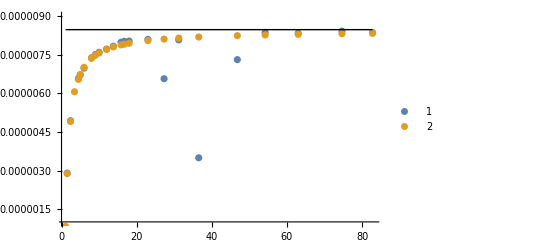

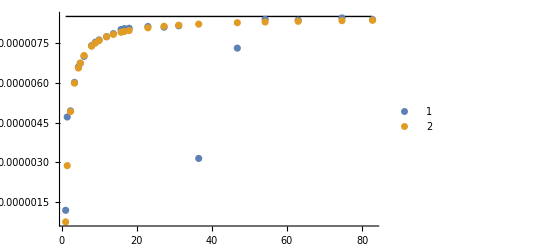

```mathematica
l1=Graphics[Line[{{aVal[[1]],Ang2[M,Gf,b0,c]},{aVal[[-1]],Ang2[M,Gf,b0,c]}}]];
l2=ListPlot[{DatAngN,DatAngSe},PlotLegends->Automatic,PlotRange->{All,{1*10^(-6), 8*10^(-6)}},Joined->False];
Show[{l2,l1},PlotRange->{All,{1*10^(-6), 9*10^(-6)}}]
```

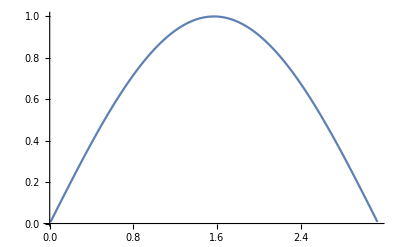

```mathematica
a=Plot[u[ϕ]/.sol1,{ϕ,ϕMin1,π/2}];
b=Plot[u[ϕ]/.sol12,{ϕ,π/2,ϕMax1}];
Show[{a,b},PlotRange->All]
```

### Contribuciones b2 caso 1, b0=Galaxia θMin=0.008

```mathematica
(*Variando b2*)
```

```mathematica
Quit[]
```

```mathematica
angu2[δ_,ϕ2_,b1_,b3_, Λ_,G_,M_,c_]:=(4 G M)/c^2(-Cos[ϕ2]/b1+(Cos[δ+ϕ2]+Sin[δ])/b3)+1/2 (G M)/c^2 Λ (4 (b1-b3 Cos[δ]) Cos[ϕ2]-(2 b1)/(1+Cos[ϕ2])+(2 b3)/(-1+Cos[δ+ϕ2])+b1 Csc[ϕ2/2]^2+b3 (Sec[(δ+ϕ2)/2]^2+4 Sin[δ] Sin[ϕ2]-2 (3+Cos[2 δ]) Sec[δ] Tan[δ]))+1/32 (G M)/c^2 Λ^2 (12 (b1^3 (Log[-Cos[ϕ2/2]]+Log[Cos[ϕ2/2]]-Log[-Sin[ϕ2/2]]-Log[Sin[ϕ2/2]])+b3^3 (Log[-Cos[1/4 (π+2 δ)]]+Log[Cos[1/4 (π+2 δ)]]-Log[-Cos[(δ+ϕ2)/2]]-Log[Cos[(δ+ϕ2)/2]]-Log[-Sin[1/4 (π+2 δ)]]-Log[Sin[1/4 (π+2 δ)]]+Log[Sin[1/2 (-δ-ϕ2)]]+Log[Sin[(δ+ϕ2)/2]]))-(Csc[δ+ϕ2]^2 Sec[δ]^2 Sin[ϕ2]^2 (b1^3 Cos[δ]^4 (-32 Cos[ϕ2]-17 Cos[3 ϕ2]+Cos[5 ϕ2]) Csc[ϕ2]^4 Sin[δ+ϕ2]^4-b3^3 (Cos[δ]^5 (-32 Cos[ϕ2]+(17-34 Cos[2 δ]) Cos[3 ϕ2]+(1-2 Cos[2 δ]+2 Cos[4 δ]) Cos[5 ϕ2])+Cos[δ]^4 (32 Sin[δ] Sin[ϕ2]+17 Sin[3 δ] Sin[3 ϕ2]-Sin[5 δ] Sin[5 ϕ2])+(-32 Sin[δ]+17 Sin[3 δ]+Sin[5 δ]) Sin[δ+ϕ2]^4)))/((-1+Cos[ϕ2]) (1+Cos[ϕ2]) (-1+Cos[δ+ϕ2]) (1+Cos[δ+ϕ2]) (-1+Sin[δ]) (1+Sin[δ])))+(G^2 M^2)/c^4(15 (b1-b3) (b1+b3) (π-2 ϕ2)+b3^2 Sin[2 ϕ2]-2 b1^2 Cos[ϕ2] Sin[2 δ+ϕ2])/(4 b1^2 b3^2)+1/8 (G^2 M^2)/c^4 Λ (Cot[ϕ2] (30-32 Csc[ϕ2]^2)+Cot[δ+ϕ2] (-30+32 Csc[δ+ϕ2]^2)+15 ((π-2 ϕ2) Csc[ϕ2]^2+(-π+2 (δ+ϕ2)) Csc[δ+ϕ2]^2-2 δ Sec[δ]^2)+2 (-14+Cos[2 δ]+Cos[2 ϕ2]+Cos[2 (δ+ϕ2)]+16 Sec[δ]^2) Tan[δ])+3/32 (G^2 M^2)/c^4 Λ^2 (-2 b3^2 Cot[δ+ϕ2] (8-47 Csc[δ+ϕ2]^2+32 Csc[δ+ϕ2]^4)+b3^2 (3 (π-2 (δ+ϕ2)) (1+4 Cos[2 (δ+ϕ2)]) Csc[δ+ϕ2]^4-1/2 Sec[δ]^5 (12 δ Cos[δ]+24 δ Cos[3 δ]+85 Sin[δ]-41 Sin[3 δ]+2 Sin[5 δ]))+1/2 b1^2 Csc[ϕ2]^5 (85 Cos[ϕ2]+41 Cos[3 ϕ2]+2 Cos[5 ϕ2]+6 (π-2 ϕ2) (Sin[ϕ2]-2 Sin[3 ϕ2]))-16 (b3^2 Cos[δ] Log[Cot[1/4 (π+2 δ)]]+b1^2 Log[Cot[ϕ2/2]] Sin[ϕ2]+b3^2 Log[Tan[(δ+ϕ2)/2]] Sin[δ+ϕ2])); (*Solución serie*)

Eq=-1-Λ̄+(Λ̄)/u[ϕ]^2+Rs Λ̄ u[ϕ]+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2==0;(*Ecuación de la geodésica*)

Ang[ϕ_,Rs_,Lb_]:=ArcTan[ -(u[ϕ] √(1-Lb/u[ϕ]^2) √(1-Rs u[ϕ]))/u'[ϕ]];
(*conversión coordenadas*)
xf[ϕ_]:=Cos[ϕ]/u[ϕ];
yf[ϕ_]:=Sin[ϕ]/u[ϕ];
```

```mathematica
(*Cantidades Físicas, Tomando una Masa solar*)
Λf =1.1056 10^-52(*10^-48*);(* 1.1056 10^-52 m^-2*)
Msun=1.9885*10^30;(*kg*)
Rsun=6.96*10^8;(*m*)
Gf=6.674*10^-11;(*m^3 kg^-1 s^-2*)
c=299792458;(*m/s*)
M=10^(12)*Msun;(*10^(12),1*)
M2=0;
RSch=2Gf M/c^2 ;(*Sch radio -> m*)
RSchF=2Gf M2/c^2;
```

```mathematica
aVal={100};
```

```mathematica
(*aVal={5, 6.1,9.5, 10,15.01, 18, 21,25, 30.315,35, 47.7,57.5,71.92, 91,107, 110,110};*) (*5,6.1, 11,15, 21,25, 30.3,40.5, 47.32,57.5,71.92,90.5,107*)(*5,6.1, 11.1,15.01, 21,25, 30.315,35, 47.7,57.5,71.92, 91,107*)
```

100

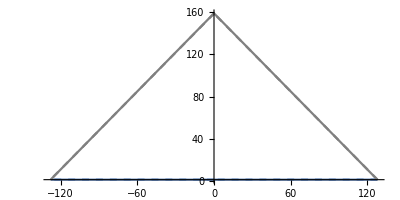

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

posición b2, b3{{ϕ→0.680039}}{ϕ→2.46155}0.008

```mathematica
DatAngN={};
DatAngSe={};
DataTriang={};
DataTriangFond={};
DatAngb2Pos={};
Do[
a=aVal[[i]];
Print[a];
(*C1*)
b0 =5*10^(20);(*m*)(*5*10^(20), 7*10^11*Rsun, Rsun*)
Rsval1=RSch/b0;(*Rs=rs/b*)
Rsval1F=RSchF/b0;(*Rs=rs/b*)
Lval1=Λf*b0^2; (*Λ̄ = Λ b^2 -> *)
ϕMin1=0.008;(*0.008*)
ϕMax1=π-ϕMin1;
δval=0;

(*Geodesic C1*)(*Print["c1"];*)

(*Metrica*)
sol1=NDSolve[{Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1[[1]];
sol12=NDSolve[{Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]; (*[π/2, ϕMax]*)

(*Fondo*)
sol1F=NDSolve[({Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1F[[1]];
sol12F=NDSolve[({Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Geodesic C2*)(*Print["c2"];*)
b1 =a*b0;(*m*)
Rsval2=RSch/b1;(*Rs=rs/b*)
Rsval2F=RSchF/b1;
Lval2=Λf*b1^2; (*Λ̄ = Λ b^2 -> *)
ϕMin2=ϕMin1;
ϕMax2=π/2;

(*Metrica*)
temp=(u[ϕMin2]*b1/b0)/.sol1[[1]];
sol2=NDSolve[{Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2},{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)

(*Fondo*)
temp=(u[ϕMin2]*b1/b0)/.sol1F[[1]];
sol2F=NDSolve[({Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2F}),{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];

(*Geodesic C2*)(*Print["c3"];*)
b2 =a*b0;(*m*)
Rsval3=RSch/b2;(*Rs=rs/b*)
Rsval3F=RSchF/b2;
Lval3=Λf*b2^2; (*Λ̄ = Λ b^2 -> *)
ϕMin3=ϕMax2;
ϕMax3=ϕMax1;

(*Metrica*)
temp=(u[ϕMax3]*b2/b0)/.sol12[[1]];
sol3=NDSolve[{Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3},{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Fondo*)
temp=(u[ϕMax3]*b2/b0)/.sol12F[[1]];
sol3F=NDSolve[({Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3F}),{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Construyendo tríangulos*)
DatTr={};
DatTrF={{},{},{}};
C1ϕvalor=Subdivide[ϕMin1,ϕMax1, 1000];
C2ϕvalor=Subdivide[ϕMin2,ϕMax2, 1000];
C3ϕvalor=Subdivide[ϕMin3,ϕMax3, 1000];
Do[
AppendTo[DatTr,{C1ϕvalor[[i]],
			    If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1[[1]],xf[C1ϕvalor[[i]]]/.sol12[[1]]], 
			    If[C1ϕvalor[[i]]<=π/2,yf[C1ϕvalor[[i]]]/.sol1[[1]],yf[C1ϕvalor[[i]]]/.sol12[[1]]],
			    C2ϕvalor[[i]],
			    b1/b0*xf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    b1/b0*yf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    C3ϕvalor[[i]],
			    b2/b0*xf[C3ϕvalor[[i]]]/.sol3[[1]],
			    b2/b0*yf[C3ϕvalor[[i]]]/.sol3[[1]]}];

(*Fondo*)
AppendTo[DatTrF,{C1ϕvalor[[i]],
			       If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1F[[1]],xf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      If[C1ϕvalor[[i]]<=π/2, yf[C1ϕvalor[[i]]]/.sol1F[[1]], yf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      C2ϕvalor[[i]],
			      b1/b0*xf[C2ϕvalor[[i]]]/.sol2F[[1]],
			      b1/b0*yf[C2ϕvalor[[i]]]/.sol2F[[1]],C3ϕvalor[[i]],
			      b2/b0*xf[C3ϕvalor[[i]]]/.sol3F[[1]], 
			      b2/b0*yf[C3ϕvalor[[i]]]/.sol3F[[1]]}];
,{i,1,Length[C1ϕvalor]}];

(*Graficandolos*)

Pc1=ParametricPlot[{xf[ϕ]/.sol1[[1]],yf[ϕ]/.sol1[[1]]},{ϕ,ϕMin1,π/2}, PlotRange->All,AspectRatio->0.5];
Pc12=ParametricPlot[{xf[ϕ]/.sol12[[1]],yf[ϕ]/.sol12[[1]]},{ϕ,π/2,ϕMax1}, PlotRange->All,AspectRatio->0.5];
Pc2=ParametricPlot[{b1/b0*xf[ϕ]/.sol2[[1]],b1/b0*yf[ϕ]/.sol2[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->Gray,AspectRatio->1];
Pc3=ParametricPlot[{b2/b0*xf[ϕ]/.sol3[[1]],b2/b0*yf[ϕ]/.sol3[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->Gray,AspectRatio->1];

Pc1F=ParametricPlot[{xf[ϕ]/.sol1F[[1]],yf[ϕ]/.sol1F[[1]]},{ϕ,ϕMin1,π/2}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc12F=ParametricPlot[{xf[ϕ]/.sol12F[[1]],yf[ϕ]/.sol12F[[1]]},{ϕ,π/2,ϕMax1}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc2F=ParametricPlot[{b1/b0*xf[ϕ]/.sol2F[[1]],b1/b0*yf[ϕ]/.sol2F[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];
Pc3F=ParametricPlot[{b2/b0*xf[ϕ]/.sol3F[[1]],b2/b0*yf[ϕ]/.sol3F[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];

Print[Show[{Pc1,Pc12,Pc2, Pc3,Pc1F,Pc12F,Pc2F,Pc3F},PlotRange->All]];

(*Calculando angulos*)
ptos={ϕMax1,π/2,ϕMin1};
(*C1*)
angC1 = Last[{Ang[ptos[[1]],Rsval1,Lval1]/.sol12,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1];
angC1F = Last[{Ang[ptos[[1]],Rsval1F,Lval1]/.sol12F,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1F];
(*C2*)
angC2= Last[{Ang[ptos[[-1]],Rsval2,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2];
angC2F = Last[{Ang[ptos[[-1]],Rsval2F,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2F];
(*C3*)
angC3= Last[{Ang[ptos[[2]],Rsval3,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3];
angC3F = Last[{Ang[ptos[[2]],Rsval3F,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3F];
(*Betas*)
betas = {angC3[[2]]-angC1[[1]], angC1[[2]]-angC2[[1]],-angC3[[1]]+angC2[[2]]};
betasF = {angC3F[[2]]-angC1F[[1]], angC1F[[2]]-angC2F[[1]],-angC3F[[1]]+angC2F[[2]]};
(*Serie*)
delI=NSolve[(u'[ϕ]/.sol2[[1]])==0,ϕ];
delI2=FindRoot[(u'[ϕ]/.sol3[[1]])==0,{ϕ,ϕMax3}];
Print["posición b2, b3",delI,delI2, ϕMin1];
delt=π/2-ϕ/.delI;
ASer=Last@angu2[delt,ϕMin1,b0,b2, Λf,Gf,M,c];
(*Salvando*)
AppendTo[DataTriang,DatTr];
AppendTo[DataTriangFond,DatTrF];
AppendTo[DatAngN,{a,Abs[Last@Total[betas-betasF]]}];
AppendTo[DatAngSe,{a,Abs@ASer}];
AppendTo[DatAngb2Pos,{a,ϕ/.delI[[1]]}],
{i, 1,Length[aVal]}(*Length[aVal]*)
]
```

```mathematica
Ang2[M_,G_,b_, c_]:=4G M/(c^2b);
```

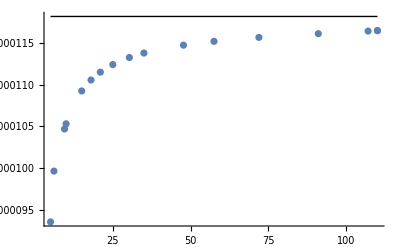

```mathematica
l1=Graphics[Line[{{aVal[[1]],Ang2[M,Gf,b0,c]},{aVal[[-1]],Ang2[M,Gf,b0,c]}}]];
l2=ListPlot[{DatAngSe},PlotLegends->Automatic,PlotRange->All,Joined->False];(*DatAngN*)
Show[{l2,l1},PlotRange->{All,All}]
```

```mathematica
{b0val[[1]],b0val[[2]],b0val[[5]],b0val[[9]], b0val[[13]],b0val[[15]]}
```

{5,5.8,10,20,60,100}

```mathematica
(*Export["dataTriang1.dat", DataTriang[[1]]]
Export["dataTriang2.dat", DataTriang[[2]]]
Export["dataTriang3.dat", DataTriang[[5]]]
Export["dataTriang4.dat", DataTriang[[9]]]
Export["dataTriang5.dat", DataTriang[[13]]]
Export["dataTriang6.dat", DataTriang[[15]]]

Export["dataTriangFond.dat", DataTriangFond[[1]]]*)
(*Export["dataAngMatheScGal.dat", DatAngN]*)
Export["dataAngSerMatheScGalL0.dat", DatAngSe]
```

dataAngSerMatheScGalL0.dat

```mathematica
term=Collect[angu2[ds,ϕs,b1s,b2s, Λs,Gs,Ms,cs],Λs]
```

```mathematica
term=(4 Gs Ms (-Cos[ϕs]/b1s+(Cos[ds+ϕs]+Sin[ds])/b2s))/cs^2+Λs^2 (1/(32 cs^4)3 Gs^2 Ms^2 (-2 b2s^2 Cot[ds+ϕs] (8-47 Csc[ds+ϕs]^2+32 Csc[ds+ϕs]^4)+b2s^2 (3 (π-2 (ds+ϕs)) (1+4 Cos[2 (ds+ϕs)]) Csc[ds+ϕs]^4-1/2 Sec[ds]^5 (12 ds Cos[ds]+24 ds Cos[3 ds]+85 Sin[ds]-41 Sin[3 ds]+2 Sin[5 ds]))+1/2 b1s^2 Csc[ϕs]^5 (85 Cos[ϕs]+41 Cos[3 ϕs]+2 Cos[5 ϕs]+6 (π-2 ϕs) (Sin[ϕs]-2 Sin[3 ϕs]))-16 (b2s^2 Cos[ds] Log[Cot[1/4 (2 ds+π)]]+b1s^2 Log[Cot[ϕs/2]] Sin[ϕs]+b2s^2 Log[Tan[(ds+ϕs)/2]] Sin[ds+ϕs]))+1/(32 cs^2)Gs Ms (12 (b1s^3 (Log[-Cos[ϕs/2]]+Log[Cos[ϕs/2]]-Log[-Sin[ϕs/2]]-Log[Sin[ϕs/2]])+b2s^3 (Log[-Cos[1/4 (2 ds+π)]]+Log[Cos[1/4 (2 ds+π)]]-Log[-Cos[(ds+ϕs)/2]]-Log[Cos[(ds+ϕs)/2]]-Log[-Sin[1/4 (2 ds+π)]]-Log[Sin[1/4 (2 ds+π)]]+Log[Sin[1/2 (-ds-ϕs)]]+Log[Sin[(ds+ϕs)/2]]))-(Csc[ds+ϕs]^2 Sec[ds]^2 Sin[ϕs]^2 (b1s^3 Cos[ds]^4 (-32 Cos[ϕs]-17 Cos[3 ϕs]+Cos[5 ϕs]) Csc[ϕs]^4 Sin[ds+ϕs]^4-b2s^3 (Cos[ds]^5 (-32 Cos[ϕs]+(17-34 Cos[2 ds]) Cos[3 ϕs]+(1-2 Cos[2 ds]+2 Cos[4 ds]) Cos[5 ϕs])+Cos[ds]^4 (32 Sin[ds] Sin[ϕs]+17 Sin[3 ds] Sin[3 ϕs]-Sin[5 ds] Sin[5 ϕs])+(-32 Sin[ds]+17 Sin[3 ds]+Sin[5 ds]) Sin[ds+ϕs]^4)))/((-1+Cos[ϕs]) (1+Cos[ϕs]) (-1+Cos[ds+ϕs]) (1+Cos[ds+ϕs]) (-1+Sin[ds]) (1+Sin[ds]))))+(Gs^2 Ms^2 (15 (b1s-b2s) (b1s+b2s) (π-2 ϕs)+b2s^2 Sin[2 ϕs]-2 b1s^2 Cos[ϕs] Sin[2 ds+ϕs]))/(4 b1s^2 b2s^2 cs^4)+Λs (1/(8 cs^4)Gs^2 Ms^2 (Cot[ϕs] (30-32 Csc[ϕs]^2)+Cot[ds+ϕs] (-30+32 Csc[ds+ϕs]^2)+15 ((π-2 ϕs) Csc[ϕs]^2+(-π+2 (ds+ϕs)) Csc[ds+ϕs]^2-2 ds Sec[ds]^2)+2 (-14+Cos[2 ds]+Cos[2 ϕs]+Cos[2 (ds+ϕs)]+16 Sec[ds]^2) Tan[ds])+(Gs Ms (4 (b1s-b2s Cos[ds]) Cos[ϕs]-(2 b1s)/(1+Cos[ϕs])+(2 b2s)/(-1+Cos[ds+ϕs])+b1s Csc[ϕs/2]^2+b2s (Sec[(ds+ϕs)/2]^2+4 Sin[ds] Sin[ϕs]-2 (3+Cos[2 ds]) Sec[ds] Tan[ds])))/(2 cs^2));
```

```mathematica
ord0=Coefficient[term, Λs,0];
ord1=Coefficient[term, Λs,1];
ord2=Coefficient[term, Λs,2];
```

```mathematica
val={ds->delt,ϕs->ϕMin1,b1s->b0,b2s->b2, Λs->Λf,Gs->Gf,Ms->M,cs->c}
```

{ds→{0.890757},ϕs→0.008,b1s→500000000000000000000,b2s→50000000000000000000000,Λs→1.1056×10^-52,Gs→6.674×10^-11,Ms→1.9885×10^42,cs→299792458}

```mathematica
fac=206265;
```

```mathematica
fac*ord0/.val
fac*Λs ord1/.val
fac*Λs^2 ord2/.val
```

{-2.40244}

{5.1104×10^-7}

{-1.68906×10^-13+0. ⅈ}

```mathematica
DatAngN
```

{{100,0.0000127531}}

```mathematica
DatAngSe
```

{{100,0.0000119533}}

```mathematica
ang=DatAngSe[[1,2]]*fac
dif=ang-Lam0*fac
porc=dif*100/ang
```

2.46556

2.46556-206265 Lam0

40.5588 (2.46556-206265 Lam0)

```mathematica
Lam0=0.000011647331364156338
```

0.0000116473

```mathematica
ListLogLinearPlot[{DatAngN,DatAngSe},PlotLegends->Automatic,PlotRange->All]
```

### Variando b0, y tomando b1, b2=1.5 b0

```mathematica
Quit[]
```

```mathematica
(* Ecuaciones Utilez *)
angu2[δ_,ϕ2_,b1_,b3_, Λ_,G_,M_,c_]:=(4 G M)/c^2(-Cos[ϕ2]/b1+(Cos[δ+ϕ2]+Sin[δ])/b3)+1/2 (G M)/c^2 Λ (4 (b1-b3 Cos[δ]) Cos[ϕ2]-(2 b1)/(1+Cos[ϕ2])+(2 b3)/(-1+Cos[δ+ϕ2])+b1 Csc[ϕ2/2]^2+b3 (Sec[(δ+ϕ2)/2]^2+4 Sin[δ] Sin[ϕ2]-2 (3+Cos[2 δ]) Sec[δ] Tan[δ]))+1/32 (G M)/c^2 Λ^2 (12 (b1^3 (Log[-Cos[ϕ2/2]]+Log[Cos[ϕ2/2]]-Log[-Sin[ϕ2/2]]-Log[Sin[ϕ2/2]])+b3^3 (Log[-Cos[1/4 (π+2 δ)]]+Log[Cos[1/4 (π+2 δ)]]-Log[-Cos[(δ+ϕ2)/2]]-Log[Cos[(δ+ϕ2)/2]]-Log[-Sin[1/4 (π+2 δ)]]-Log[Sin[1/4 (π+2 δ)]]+Log[Sin[1/2 (-δ-ϕ2)]]+Log[Sin[(δ+ϕ2)/2]]))-(Csc[δ+ϕ2]^2 Sec[δ]^2 Sin[ϕ2]^2 (b1^3 Cos[δ]^4 (-32 Cos[ϕ2]-17 Cos[3 ϕ2]+Cos[5 ϕ2]) Csc[ϕ2]^4 Sin[δ+ϕ2]^4-b3^3 (Cos[δ]^5 (-32 Cos[ϕ2]+(17-34 Cos[2 δ]) Cos[3 ϕ2]+(1-2 Cos[2 δ]+2 Cos[4 δ]) Cos[5 ϕ2])+Cos[δ]^4 (32 Sin[δ] Sin[ϕ2]+17 Sin[3 δ] Sin[3 ϕ2]-Sin[5 δ] Sin[5 ϕ2])+(-32 Sin[δ]+17 Sin[3 δ]+Sin[5 δ]) Sin[δ+ϕ2]^4)))/((-1+Cos[ϕ2]) (1+Cos[ϕ2]) (-1+Cos[δ+ϕ2]) (1+Cos[δ+ϕ2]) (-1+Sin[δ]) (1+Sin[δ])))+(G^2 M^2)/c^4(15 (b1-b3) (b1+b3) (π-2 ϕ2)+b3^2 Sin[2 ϕ2]-2 b1^2 Cos[ϕ2] Sin[2 δ+ϕ2])/(4 b1^2 b3^2)+1/8 (G^2 M^2)/c^4 Λ (Cot[ϕ2] (30-32 Csc[ϕ2]^2)+Cot[δ+ϕ2] (-30+32 Csc[δ+ϕ2]^2)+15 ((π-2 ϕ2) Csc[ϕ2]^2+(-π+2 (δ+ϕ2)) Csc[δ+ϕ2]^2-2 δ Sec[δ]^2)+2 (-14+Cos[2 δ]+Cos[2 ϕ2]+Cos[2 (δ+ϕ2)]+16 Sec[δ]^2) Tan[δ])+3/32 (G^2 M^2)/c^4 Λ^2 (-2 b3^2 Cot[δ+ϕ2] (8-47 Csc[δ+ϕ2]^2+32 Csc[δ+ϕ2]^4)+b3^2 (3 (π-2 (δ+ϕ2)) (1+4 Cos[2 (δ+ϕ2)]) Csc[δ+ϕ2]^4-1/2 Sec[δ]^5 (12 δ Cos[δ]+24 δ Cos[3 δ]+85 Sin[δ]-41 Sin[3 δ]+2 Sin[5 δ]))+1/2 b1^2 Csc[ϕ2]^5 (85 Cos[ϕ2]+41 Cos[3 ϕ2]+2 Cos[5 ϕ2]+6 (π-2 ϕ2) (Sin[ϕ2]-2 Sin[3 ϕ2]))-16 (b3^2 Cos[δ] Log[Cot[1/4 (π+2 δ)]]+b1^2 Log[Cot[ϕ2/2]] Sin[ϕ2]+b3^2 Log[Tan[(δ+ϕ2)/2]] Sin[δ+ϕ2])); (*Solución serie*)

Eq=-1-Λ̄+(Λ̄)/u[ϕ]^2+Rs Λ̄ u[ϕ]+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2==0;(*Ecuación de la geodésica*)

Ang[ϕ_,Rs_,Lb_]:=ArcTan[ -(u[ϕ] √(1-Lb/u[ϕ]^2) √(1-Rs u[ϕ]))/u'[ϕ]];
(*conversión coordenadas*)
xf[ϕ_]:=Cos[ϕ]/u[ϕ];
yf[ϕ_]:=Sin[ϕ]/u[ϕ];
```

```mathematica
(*Cantidades Físicas, Tomando una Masa solar*)
Λf =0*10^-20;(*1.1056 10^-52 m^-2*)
Msun=1.9885*10^30;(*kg*)
Rsun=6.96*10^8;(*m*)
Gf=6.674*10^-11;(*m^3 kg^-1 s^-2*)
c=299792458;(*m/s*)
M=100*Msun;(*100, 1*)
M2=0;
RSch=2Gf M/c^2 ;(*Sch radio -> m*)
RSchF=2Gf M2/c^2;
```

```mathematica
a=1.5; (*factor multiplicativo para d2, d3*)
```

```mathematica
b0val={800,850,900,950, 1000,1250,1500,1750,1800,1850, 5000, 5500, 5600, 5700, 5800, 5900, 8250, 8500, 8800, 9750}; (*{4.15, 4.2, 4.3, 4.4, 4.6, 4.7, 5,5.8,7,9,10,11,14,15,20,30,40,50,80,100,150,450, 470, 480, 500, 650,700, 800, 1000, 3500, 3900}*)(*valores del parámtro de impacto b0*)
(*{800,850,900,950, 1000,1250,1500,1750,1800,1850, 5000, 5500, 5600, 5700, 5800, 5900, 8250, 8500, 8800, 9750}*)
```

1

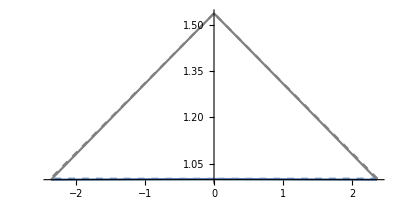

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

posición b2, b3{{ϕ→1.34601}}{ϕ→1.79558}0.4

2

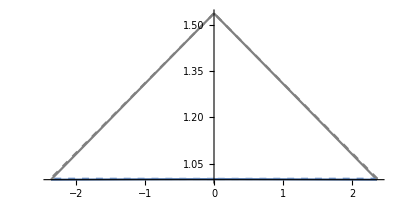

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

posición b2, b3{{ϕ→1.34609}}{ϕ→1.79551}0.4

3

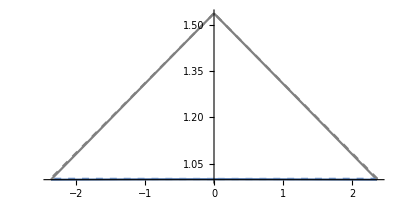

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve::ifun will be suppressed during this calculation.

posición b2, b3{{ϕ→1.34615}}{ϕ→1.79544}0.4

4

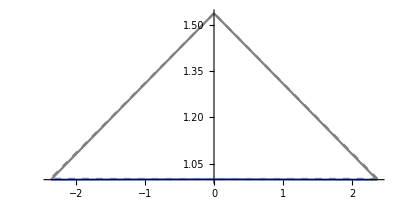

posición b2, b3{{ϕ→1.34621}}{ϕ→1.79538}0.4

5

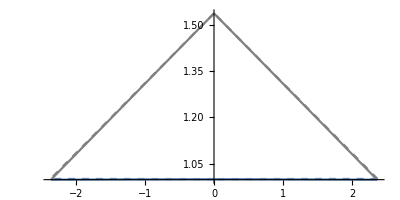

posición b2, b3{{ϕ→1.34627}}{ϕ→1.79533}0.4

6

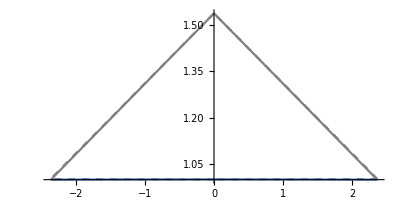

posición b2, b3{{ϕ→1.34647}}{ϕ→1.79512}0.4

7

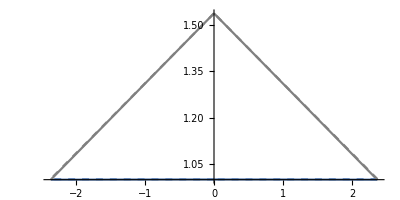

posición b2, b3{{ϕ→1.34661}}{ϕ→1.79498}0.4

8

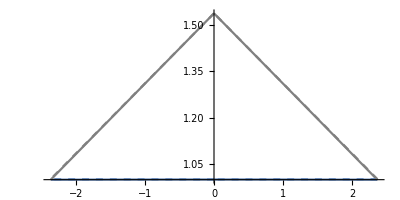

posición b2, b3{{ϕ→1.34671}}{ϕ→1.79488}0.4

9

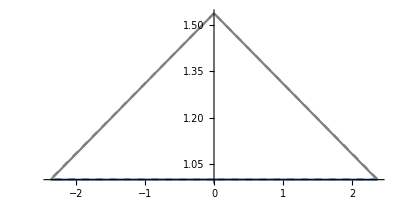

posición b2, b3{{ϕ→1.34673}}{ϕ→1.79487}0.4

10

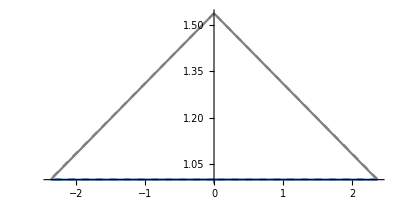

posición b2, b3{{ϕ→1.34674}}{ϕ→1.79485}0.4

11

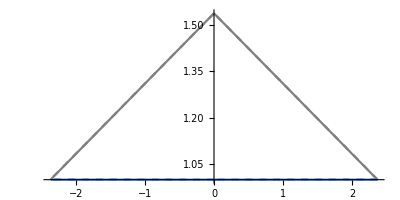

posición b2, b3{{ϕ→1.34709}}{ϕ→1.7945}0.4

12

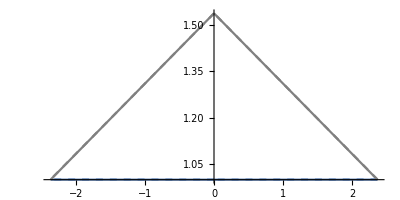

posición b2, b3{{ϕ→1.34711}}{ϕ→1.79448}0.4

13

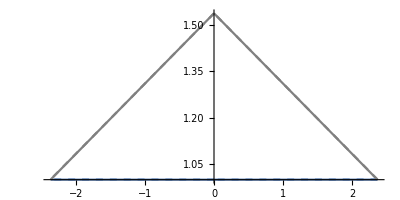

posición b2, b3{{ϕ→1.34711}}{ϕ→1.79448}0.4

14

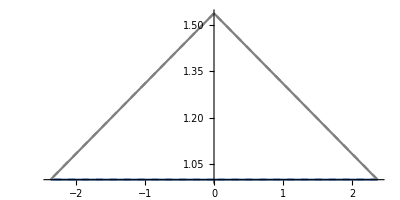

posición b2, b3{{ϕ→1.34712}}{ϕ→1.79448}0.4

15

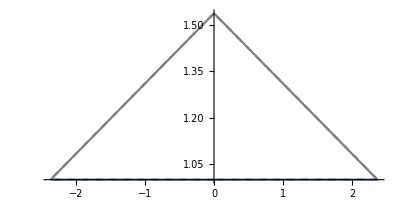

posición b2, b3{{ϕ→1.34712}}{ϕ→1.79447}0.4

16

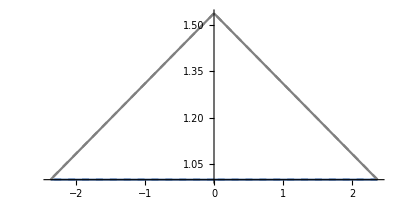

posición b2, b3{{ϕ→1.34712}}{ϕ→1.79447}0.4

17

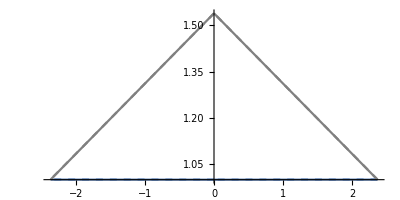

posición b2, b3{{ϕ→1.34717}}{ϕ→1.79442}0.4

18

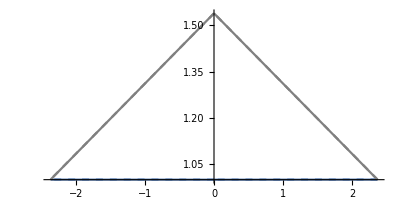

posición b2, b3{{ϕ→1.34718}}{ϕ→1.79442}0.4

19

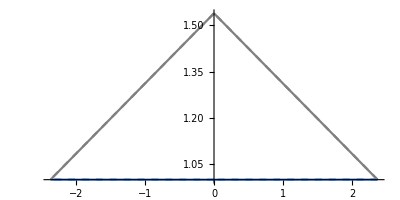

posición b2, b3{{ϕ→1.34718}}{ϕ→1.79441}0.4

20

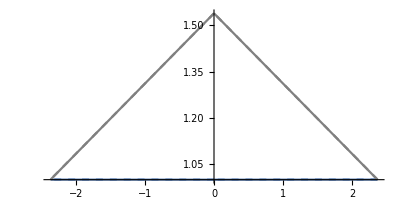

posición b2, b3{{ϕ→1.34719}}{ϕ→1.7944}0.4

```mathematica
DatAngN={};
DatAngSe={};
DataTriang={};
DataTriangFond={};
Do[
b=b0val[[i]];
Print[i];
(*C1*)
b0 =b*RSch;(*m*)
Rsval1=RSch/b0;(*Rs=rs/b*)
Rsval1F=RSchF/b0;(*Rs=rs/b*)
Lval1=Λf*b0^2; (*Λ̄ = Λ b^2 -> *)
ϕMin1=0.4;
ϕMax1=π-ϕMin1;
δval=0;

(*Geodesic C1*)(*Print["c1"];*)

(*Metrica*)
sol1=NDSolve[{Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];(*0.000095*)(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1[[1]];
sol12=NDSolve[{Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]; (*[π/2, ϕMax]*)

(*Fondo*)
sol1F=NDSolve[({Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1F[[1]];
sol12F=NDSolve[({Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]; (*[π/2, ϕMax]*)

(*Geodesic C2*)(*Print["c2"];*)
b1 =a*b0;(*m*)
Rsval2=RSch/b1;(*Rs=rs/b*)
Rsval2F=RSchF/b1;
Lval2=Λf*b1^2; (*Λ̄ = Λ b^2 -> *)
ϕMin2=ϕMin1;
ϕMax2=π/2;

(*Metrica*)
temp=(u[ϕMin2]*b1/b0)/.sol1[[1]];
sol2=NDSolve[{Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2},{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];(*[ϕMmin, π/2]*)

(*Fondo*)
temp=(u[ϕMin2]*b1/b0)/.sol1F[[1]];
sol2F=NDSolve[({Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2F}),{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];

(*Geodesic C2*)(*Print["c3"];*)
b2 =a*b0;(*m*)
Rsval3=RSch/b2;(*Rs=rs/b*)
Rsval3F=RSchF/b2;
Lval3=Λf*b2^2; (*Λ̄ = Λ b^2 -> *)
ϕMin3=ϕMax2;
ϕMax3=ϕMax1;

(*Metrica*)
temp=(u[ϕMax3]*b2/b0)/.sol12[[1]];
sol3=NDSolve[{Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3},{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]; (*[π/2, ϕMax]*)

(*Fondo*)
temp=(u[ϕMax3]*b2/b0)/.sol12F[[1]];
sol3F=NDSolve[({Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3F}),{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]; (*[π/2, ϕMax]*)

(*Construyendo tríangulos*)
DatTr={};
DatTrF={{},{},{}};
C1ϕvalor=Subdivide[ϕMin1,ϕMax1, 1000];
C2ϕvalor=Subdivide[ϕMin2,ϕMax2, 1000];
C3ϕvalor=Subdivide[ϕMin3,ϕMax3, 1000];
Do[
AppendTo[DatTr,{C1ϕvalor[[i]],
			    If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1[[1]],xf[C1ϕvalor[[i]]]/.sol12[[1]]], 
			    If[C1ϕvalor[[i]]<=π/2,yf[C1ϕvalor[[i]]]/.sol1[[1]],yf[C1ϕvalor[[i]]]/.sol12[[1]]],
			    C2ϕvalor[[i]],
			    b1/b0*xf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    b1/b0*yf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    C3ϕvalor[[i]],
			    b2/b0*xf[C3ϕvalor[[i]]]/.sol3[[1]],
			    b2/b0*yf[C3ϕvalor[[i]]]/.sol3[[1]]}];

(*Fondo*)
AppendTo[DatTrF,{C1ϕvalor[[i]],
			       If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1F[[1]],xf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      If[C1ϕvalor[[i]]<=π/2, yf[C1ϕvalor[[i]]]/.sol1F[[1]], yf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      C2ϕvalor[[i]],
			      b1/b0*xf[C2ϕvalor[[i]]]/.sol2F[[1]],
			      b1/b0*yf[C2ϕvalor[[i]]]/.sol2F[[1]],C3ϕvalor[[i]],
			      b2/b0*xf[C3ϕvalor[[i]]]/.sol3F[[1]], 
			      b2/b0*yf[C3ϕvalor[[i]]]/.sol3F[[1]]}];
,{i,1,Length[C1ϕvalor]}];

(*Graficandolos*)

Pc1=ParametricPlot[{xf[ϕ]/.sol1[[1]],yf[ϕ]/.sol1[[1]]},{ϕ,ϕMin1,π/2}, PlotRange->All,AspectRatio->0.5];
Pc12=ParametricPlot[{xf[ϕ]/.sol12[[1]],yf[ϕ]/.sol12[[1]]},{ϕ,π/2,ϕMax1}, PlotRange->All,AspectRatio->0.5];
Pc2=ParametricPlot[{b1/b0*xf[ϕ]/.sol2[[1]],b1/b0*yf[ϕ]/.sol2[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->Gray,AspectRatio->1];
Pc3=ParametricPlot[{b2/b0*xf[ϕ]/.sol3[[1]],b2/b0*yf[ϕ]/.sol3[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->Gray,AspectRatio->1];

Pc1F=ParametricPlot[{xf[ϕ]/.sol1F[[1]],yf[ϕ]/.sol1F[[1]]},{ϕ,ϕMin1,π/2}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc12F=ParametricPlot[{xf[ϕ]/.sol12F[[1]],yf[ϕ]/.sol12F[[1]]},{ϕ,π/2,ϕMax1}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc2F=ParametricPlot[{b1/b0*xf[ϕ]/.sol2F[[1]],b1/b0*yf[ϕ]/.sol2F[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];
Pc3F=ParametricPlot[{b2/b0*xf[ϕ]/.sol3F[[1]],b2/b0*yf[ϕ]/.sol3F[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];

Print[Show[{Pc1,Pc12,Pc2, Pc3,Pc1F,Pc12F,Pc2F,Pc3F},PlotRange->All]];

(*Calculando angulos*)
ptos={ϕMax1,π/2,ϕMin1};
(*C1*)
angC1 = Last[{Ang[ptos[[1]],Rsval1,Lval1]/.sol12,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1];
angC1F = Last[{Ang[ptos[[1]],Rsval1F,Lval1]/.sol12F,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1F];
(*C2*)
angC2= Last[{Ang[ptos[[-1]],Rsval2,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2];
angC2F = Last[{Ang[ptos[[-1]],Rsval2F,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2F];
(*C3*)
angC3= Last[{Ang[ptos[[2]],Rsval3,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3];
angC3F = Last[{Ang[ptos[[2]],Rsval3F,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3F];
(*Betas*)
betas = {angC3[[2]]-angC1[[1]], angC1[[2]]-angC2[[1]],-angC3[[1]]+angC2[[2]]};
betasF = {angC3F[[2]]-angC1F[[1]], angC1F[[2]]-angC2F[[1]],-angC3F[[1]]+angC2F[[2]]};

(*Serie*)
delI=NSolve[(u'[ϕ]/.sol2[[1]])==0,ϕ];
delI2=FindRoot[(u'[ϕ]/.sol3[[1]])==0,{ϕ,ϕMax3}];
Print["posición b2, b3",delI,delI2, ϕMin1];
delt=π/2-ϕ/.delI;
ASer=Last@angu2[delt,ϕMin1,b0,b2, Λf,Gf,M,c];

(*Salvando*)
AppendTo[DataTriang,DatTr];
AppendTo[DataTriangFond,DatTrF];
AppendTo[DatAngN,{b,Abs[Last@Total[betas-betasF]]}];
AppendTo[DatAngSe,{b,Abs@ASer}],
{i, 1,Length[b0val]}
]
```

```mathematica
{b0val[[1]],b0val[[2]],b0val[[5]],b0val[[9]], b0val[[13]],b0val[[15]]}
```

{5,5.8,10,20,60,100}

```mathematica
(*Export["dataTriang1.dat", DataTriang[[1]]]
Export["dataTriang2.dat", DataTriang[[2]]]
Export["dataTriang3.dat", DataTriang[[5]]]
Export["dataTriang4.dat", DataTriang[[9]]]
Export["dataTriang5.dat", DataTriang[[13]]]
Export["dataTriang6.dat", DataTriang[[15]]]

Export["dataTriangFond.dat", DataTriangFond[[1]]]*)
Export["dataAngMathe100ML0part2.dat", DatAngN]
Export["dataAngSerMathe100ML0part2.dat", DatAngSe]
```

dataAngMathe100ML0part2.dat

dataAngSerMathe100ML0part2.dat

```mathematica
DatAngN
```

{{800,0.000466535},{850,0.000439156},{900,0.000414731},{950,0.000392881},{1000,0.000373219},{1250,0.000298053},{1500,0.00024848},{1750,0.000213061},{1800,0.000207156},{1850,0.00020157},{5000,0.0000744536},{5500,0.0000676841},{5600,0.0000664753},{5700,0.0000653088},{5800,0.0000641827},{5900,0.0000630946},{8250,0.0000451199},{8500,0.0000437927},{8800,0.0000422995},{9750,0.0000381775}}

```mathematica
test={{800,0.00046130641413311135},{850,0.00042121414402873647},{900,0.00042016992042348544},{950,0.00039035876977389083},{1000,0.00034824391541732336},{1250,0.0003009339156872515},{1500,0.00024380737598789226},{1750,0.00022586638490196265},{1800,0.00021655114982360724},{1850,0.00020480427941349522},{5000,0.02692520590062142},{5500,0.00005565692756087648},{5600,0.00007589214008901779},{5700,0.00007655982425824881},{5800,0.00007546580141731818},{5900,0.00007333603546888501},{8250,0.00003704719480562835},{8500,0.00005863634437169862},{8800,0.00002319204779560602},{9750,0.00005476380690611071}};
```

```mathematica
DatAngN-test
```

{{0,5.22841×10^-6},{0,0.0000179417},{0,-5.43878×10^-6},{0,2.5218×10^-6},{0,0.0000249752},{0,-2.88052×10^-6},{0,4.67245×10^-6},{0,-0.0000128057},{0,-9.39544×10^-6},{0,-3.23475×10^-6},{0,-0.0268508},{0,0.0000120272},{0,-9.41687×10^-6},{0,-0.000011251},{0,-0.0000112831},{0,-0.0000102414},{0,8.07271×10^-6},{0,-0.0000148437},{0,0.0000191075},{0,-0.0000165863}}

```mathematica
DatAngSe
```

{{800,0.000581237},{850,0.000546988},{900,0.000516551},{950,0.000489322},{1000,0.000464821},{1250,0.000371748},{1500,0.00030973},{1750,0.000265446},{1800,0.000258067},{1850,0.000251086},{5000,0.0000928558},{5500,0.0000844121},{5600,0.0000829044},{5700,0.0000814495},{5800,0.0000800449},{5900,0.0000786879},{8250,0.0000562698},{8500,0.0000546145},{8800,0.0000527523},{9750,0.0000476116}}

```mathematica
test2={{800,0.0005800157079010629},{850,0.0005456901888774883},{900,0.0005151732508851223},{950,0.0004878713011847561},{1000,0.0004632954770474071},{1250,0.0003698447976661291},{1500,0.0003074588906295957},{1750,0.0002628030364816994},{1800,0.00025535301956651485},{1850,0.0002483038765177348},{5000,0.00008630337795018938},{5500,0.0000774820285590462},{5600,0.00007590845724568089},{5700,0.00007439148898225538},{5800,0.00007292892821600654},{5900,0.00007151784222245046},{8250,0.00004917939815394215},{8500,0.00004771977624400301},{8800,0.000046153348717137316},{9750,0.00004240761089503974}};
```

```mathematica
test2-DatAngSe
```

{{0,-1.2215×10^-6},{0,-1.29808×10^-6},{0,-1.37766×10^-6},{0,-1.45108×10^-6},{0,-1.52517×10^-6},{0,-1.90362×10^-6},{0,-2.27123×10^-6},{0,-2.64306×10^-6},{0,-2.7136×10^-6},{0,-2.78247×10^-6},{0,-6.55243×10^-6},{0,-6.93011×10^-6},{0,-6.99592×10^-6},{0,-7.05806×10^-6},{0,-7.11596×10^-6},{0,-7.17002×10^-6},{0,-7.09038×10^-6},{0,-6.89473×10^-6},{0,-6.59899×10^-6},{0,-5.20398×10^-6}}

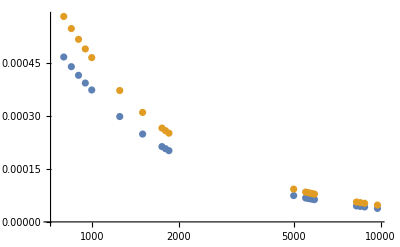

```mathematica
ListLogLinearPlot[{DatAngN,DatAngSe}]
```

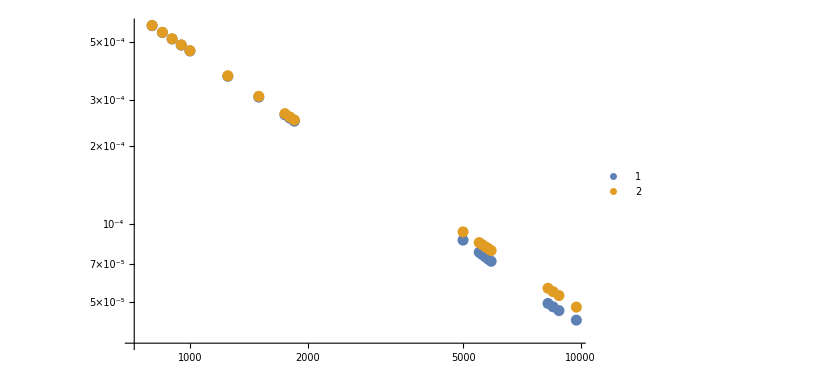

```mathematica
ListLogLogPlot[{test2,DatAngSe},PlotLegends->Automatic]
```